## more

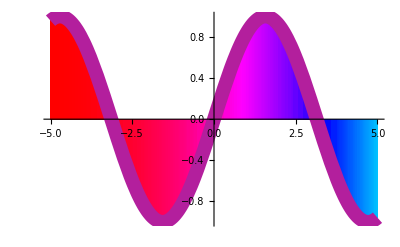

```mathematica
Plot[{Sin[x],Sin[x]},{x,-5,5},PlotStyle ->{ Directive[Thickness[0.025],GrayLevel[.05]],None},
ColorFunction->{Function[x,Hue[Cos[x]]],Black},Filling->Axis]
```

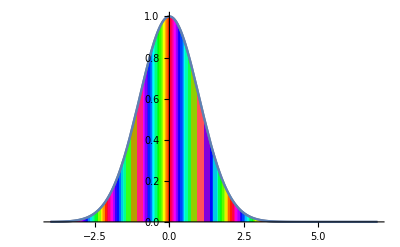

```mathematica
QArgColorPlot[ⅇ^(-ⅈ 6 x-x^2/2),{x,-4,7}]
```

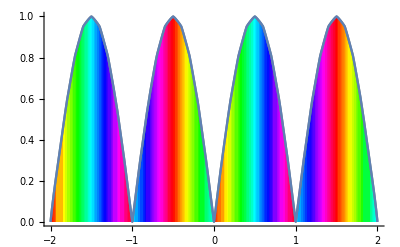

```mathematica
mytab=Table[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2,0.1}];
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{-2,2}]
```

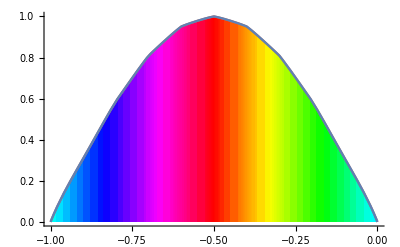

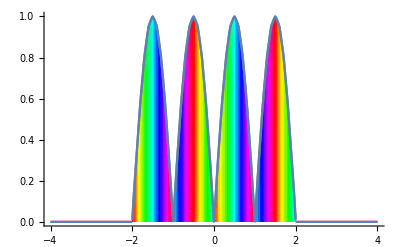

```mathematica
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{{-2,2},{-1,0}}]
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{{-2,2},{-4,4}}]
```

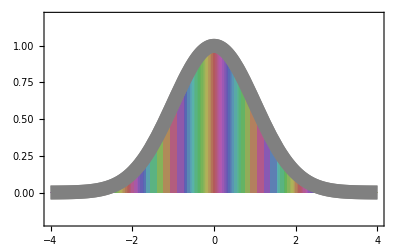

```mathematica
QArgColorPlot[ⅇ^(-ⅈ 6 x-x^2/2),{x,-4,4},PlotStyle->{Thickness[0.025],GrayLevel[0.5]},QSaturation->0.5,QBrightness->0.7,PlotRange->{-0.2,1.2},Frame->True,Axes->{True,False}]
```

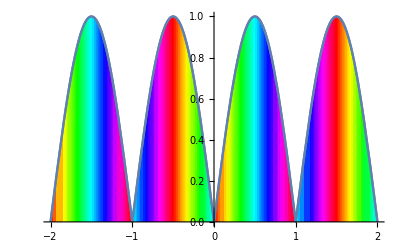

```mathematica
mytab=Table[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2,0.1}];
QArgColorPlot[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2},Axes->True,QHorizontalRange->{-2,2}]
```

```mathematica
QArgColorPlot[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2},Axes->True,QHorizontalRange->{{-2,2},{-1,0}}]
QArgColorPlot[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2},Axes->True,QHorizontalRange->{{-2,2},{-4,4}}]
```

-Graphics-

-Graphics-

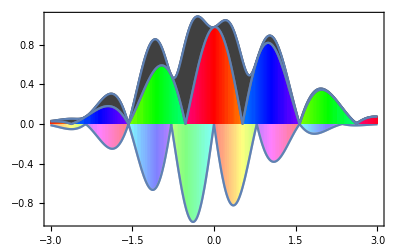

```mathematica
spinorfunction[x_]:={Cos[3 x] ⅇ^(-1/3 (x-1/4)^2+ⅈ x),Sin[4 x] ⅇ^(-1/2 (x+1/4)^2+2 ⅈ x)}
QSpinorPlot[Evaluate[spinorfunction[x]],{x,-3.,3.},PlotRange->All,Frame->True,Axes->{True,False}]
```

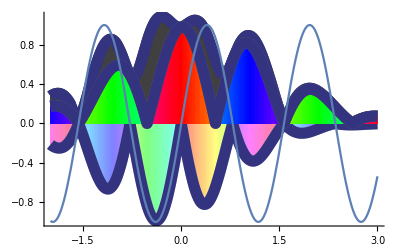

```mathematica
spinorlist=Table[{x,spinorfunction[x]},{x,-3,3,0.1}];
QListSpinorCombinedPlot[{spinorlist,Sin[4 x]},{x,-2,3},PlotRange->All,QCurveStyle->{RGBColor[0,0.7,0.9],Thickness[0.03]},PlotStyle->{RGBColor[0.2,0.2,0.5],Thickness[0.02]}]
```

## QuantumKernel2D tests:

```mathematica
pos = {-3., -3.}; mom = {4., 4.}; a = 1.; 
Gauss[x0_, y0_, kx_, ky_, a_] := Compile @@ 
       {{x, y}, Simplify[(a/Pi)^(1/2)*Exp[I*(kx*x + ky*y)]*
             Exp[-((a*((x - x0)^2 + (y - y0)^2))/2)]]}; 
f = Gauss[pos[[1]], pos[[2]], mom[[1]], mom[[2]], 1]; 
numleft = {-7., -7.}; numright = {7., 7.}; 
dx = 0.14; 
psi0 = Table[f[x, y], {y, numleft[[2]] + dx/2, numright[[2]] - dx/2, dx}, 
       {x, numleft[[1]] + dx/2, numright[[1]] - dx/2, dx}]; 
psi = QNewFunction[Re[psi0], Im[psi0]]; 
Emean = mom.mom/2;
potfnc = Compile[{x, y}, Emean/Cosh[2(x+y)]];V0 = Table[potfnc[x,y],
      {y,numleft[[2]]+dx/2,numright[[2]]-dx/2,dx},
      {x,numleft[[1]]+dx/2,numright[[1]]-dx/2,dx}];
V = QNewFunction[Re[V0],Im[V0]];
H = QSchroedinger2D[V, None, None, 1., 1., dx];
dt = 0.01; ordr = 4; reps = 20;
QTimeEvolution[H, psi, dt, ordr, reps];
```

```mathematica
psi1 = QGetArray[psi];
psi2 = psi1[[1]] + I psi1[[2]];
QListComplexDensityPlot[psi2,Mesh->False,DataRange->{{-7,7},{-7,7}},QSphereRadius->1/3.,ImageSize->100]
```

QListComplexDensityPlot[$Failed+ⅈ Reverse[$Failed],Mesh→False,DataRange→{{-7,7},{-7,7}},QSphereRadius→0.333333,ImageSize→100]

```mathematica
QTimeEvolution[H, psi, dt, ordr, 80];
psi1 = QGetArray[psi];
psi2 = psi1[[1]] + I*psi1[[2]]; 
QListComplexDensityPlot[psi2, Mesh -> False, DataRange -> {{-7, 7}, {-7, 7}}, 
  QSphereRadius -> 1/3., ImageSize -> 100]
```

-Graphics-

```mathematica
psi
abspsi = QGetAbsArray[psi]; 
Row[{ListDensityPlot[abspsi, Mesh -> False, PlotRange -> {0, 0.4}], ListDensityPlot[abspsi^2, Mesh -> False, PlotRange -> {0, 0.4^2}]}]
```

QFunctionObject[1]

ListDensityPlot[ArrayReshape[$Failed,Most[$Failed]],Mesh→False,PlotRange→{0,0.4}]ListDensityPlot[ArrayReshape[$Failed,Most[$Failed]]^2,Mesh→False,PlotRange→{0,0.16}]

```mathematica
abspsi
```

ArrayReshape[$Failed,Most[$Failed]]

```mathematica
??QGetAbsList
```

QGetAbsList[f]. Package: VQM`QuantumKernel`.

QGetAbsList[function_]:=ExternalCall[LinkObject[…],CallPacket[8,{function}]]

```mathematica
QGetAbsList[psi]
```

$Failed